# Design and Implementation of an Automated Analysis and Reporting System

Dylan Boliske

## Abstract

Often times, designing or working with large analytics systems can be more difficult and time consuming than deciding on the actual analysis. In this presentation we’ll look at a case study of building a media monitoring and reporting system from the ground up, that was purpose built for use by Wolfram’s in-house Public Relations department in just a few hours.

## Table of Contents

System Design

General Task Design

Data Collection

Cleaning and Processing

Generating Visualizations and Statistics

Building Reports and Dashboards

Publishing and Sharing

## System Design

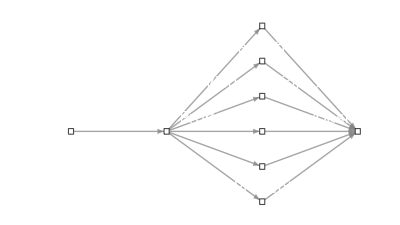

```mathematica
Graph[{"Data Collection"->"Cleaning and Processing","Cleaning and Processing"->"Visualization 1","Cleaning and Processing"->"Visualization 2","Cleaning and Processing"->"Visualization 3","Cleaning and Processing"->"Visualization 4","Cleaning and Processing"->"...","Cleaning and Processing"->"Data Presentation",
"Visualization 1"->"Dashboard",
"Visualization 2"->"Dashboard",
"Visualization 3"->"Dashboard",
"Visualization 4"->"Dashboard",
"..."->"Dashboard",
"Data Presentation"->"Dashboard"},
BaseStyle->{FontSize->16},
EdgeStyle->Gray,
ImageSize->Full,
VertexCoordinates->{{0,1},{1,1},{2,2},{2,5/3},{2,4/3},{2,1},{2,2/3},{2,1/3},{3,1}},
VertexLabels->Placed["Name",Above],
VertexShapeFunction->"Square",
VertexStyle->White
]
```

## General Task Design

All tasks in this system follow the same basic layout:

```mathematica
ScheduledTask[
	Module[{},
		Get["package/containing/task-specific-code"];
		TaskSpecificFunction["system/configuration/file"]
	],
	"Daily",
	NotificationFunction :> Get["list/of/system/admins"]
]
```

Deploying tasks with expressions like this makes it easier to make modifications to specific aspects of the task. Examples:

If the schedule of the task changes, simply redeploy the task with the same code and new schedule.

If the code being executed needs to change, simply update the package. The new code will be executed on the next task execution.

If admins are added/removed, then update the file with the list of system administrators and notifications will be sent out to the correct people.

## Data Collection

This phase focuses on collecting data from external resources, whether they be through ServiceConnect, URLRead, DataDrop, etc.

```mathematica
raw = URLRead[
	HTTPRequest[
		"http://webhose.io/filterWebContent",
		<|
			"Query" -> {
				"token" -> ,
				"format" -> "json",
				"sort" -> "crawled",
				"q" -> StringRiffle[
					{
						"text:\"Halloween\"",
						"language:english",
						"is_first:true",
						"domain_rank:<5000",
						StringJoin[{"published:>", }]
					},
					" "
				]
			}
		|>
	],
	"Body"
];
posts = Lookup[
	ImportString[
		ToString[raw, CharacterEncoding -> "UTF-8"],
		"JSON"
	],
	"posts"
];
dataset = Dataset[
	Replace[
		posts,
		{r__Rule} :> Association[r],
		Infinity
	]
]
```

## Cleaning and Processing

This phase focuses on cleaning and doing any ‘universal’ processing. We handle this separately from collection in order to avoid loss of data if something goes wrong and in order to preserve the raw data for possible future analysis.

The final goal of this task is to export the data into whatever the final storage location is going to be, e.g. a file, a database, a ResourceObject, etc.

```mathematica
filtered = dataset[All,][All,MapAt[,#,{Key["thread"]}]&]
```

```mathematica
formattedValue["Timestamp"]=;
formattedValue["Title"]=;
formattedValue["Author"]=;
formattedValue["Text"]=;
formattedValue["URL"]=;
formattedValue["Type"]=;
formattedValue["Country"]=;
formattedValue["Language"]=;
formattedValue["Counts"]=;
formattedValue["Scores"]=;
formattedValue["DomainRank"]=;
formattedValue["Social"]=;
```

```mathematica
sorted = SortBy[
	Map[
		Association[
			Through[
				Table[formattedValue[key],{key,}][#,"Halloween"]
			]
		]&,
		filtered
	],
	#["Timestamp"]&
]
```

## Generating Visualizations and Statistics

Like in the previous steps, we break down the tasks into individual components. This is for multiple reasons:

Like before, it avoids catastrophic failure

Allows for longer computations

Allows for multiple consumers in different ways

```mathematica
With[{times = sorted[All,"Timestamp"]},
	DateHistogram[
		times,
		Quantity[10,"Minutes"],
		
	]
]
```

## Building Reports and Dashboards

This comes down to the best ways to consume the results of your analytics in the previous steps.

DocumentGenerators work for creating notebooks based on a template notebook and are run on a schedule similar to a ScheduledTask. Deploying one produces a bundle of objects that handle generating the report, archiving old reports, and sending out copies of the report as specified.

```mathematica
CloudDeploy[
	DocumentGenerator[
		(* Template Notebook *),
		(* Driver Details [optional] *),
		(* Schedule *),
		DeliveryFunction->(* Report Consumers *),
		NotificationFunction->(* System Admins *)
	],
	"wtc/2019/talk/report"
]
```

For a raw HTML page, Delayed can be used to build a page that imports the latest charts.

```mathematica
CloudDeploy[
	Delayed[
		XMLTemplate[(* Template code *)][(* Computed values *)],
		"HTML"
	],
	"wtc/2019/talk/webpage",
	Permissions -> (* Report Consumers *)
]
```

A new alternative is to do a bit of both by using the Wolfram Notebook Embedder to put the notebook generated by the DocumentGenerator into a web page.

## Publishing and Sharing

Since consumers of reports and admins can change, creating a PermissionsGroup or a PermissionsKey can be a simple way to regulate who has access to a report without needing to redeploy any parts of the system.

Beyond those, if the report is meant to be public, CloudPublish can be used to deploy results to an independent, public object.

In most other cases, you can also use SetPermissions to modify the permissions on an individual instance.

## Source Code

Example system available on GitHub along with these slides:

-Graphics-